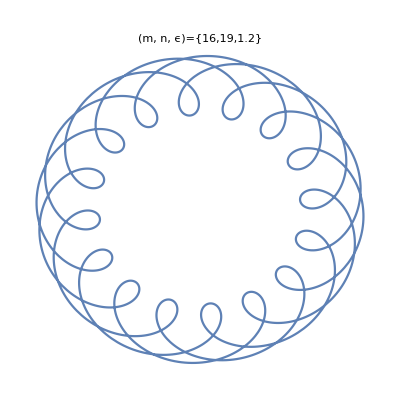

```mathematica
Clear["Global`*"];
(* m degrees of rotational symmetry *)
plotCurve[m0_, n0_, ϵ0_] := Module[{m = m0, n = n0, ϵ = ϵ0},
v =m/n; θ0 = 0; tf = 2Pi n;
l[θ_] = ϵ Sin[v ( θ- θ0)] ;
r[θ_] = Exp[l[θ]];
sol2=NDSolve[{β1'[θ] == Cos[θ]r[θ],β2'[θ]==Sin[θ]r[θ] ,β1[0]==0,β2[0]==0},{β1,β2},{θ,0,tf}];
sol[t_] = {β1[t],β2[t]}/.sol2[[1]];
ParametricPlot[sol[θ],{θ,0,tf},Axes->False,PlotLabel->HoldForm["(m, n, ϵ)"={m0,n0,ϵ0}]]
];

(* Plots the sum of (m0, n0, ϵ0) and (m1, n1, ϵ1) *)
plotSum[m0_, n0_, ϵ0_, m1_, n1_, ϵ1_] := Module[{ma = m0, na = n0, ϵa = ϵ0, mb = m1, nb = n1, ϵb = ϵ1},
θ0 = 0; tf =2 Pi Max[na,nb];
va =ma/na; vb = mb/nb;
la[θ_] = ϵa Sin[va ( θ- θ0)] ;
lb[θ_] = ϵb Sin[vb ( θ- θ0)] ;
l[θ_] = la[θ]+lb[θ];
r[θ_] = Exp[l[θ]];
sol2=NDSolve[{β1'[θ] == Cos[θ]r[θ],β2'[θ]==Sin[θ]r[θ] ,β1[0]==0,β2[0]==0},{β1,β2},{θ,0,tf},AccuracyGoal->10, PrecisionGoal->10,MaxSteps->10000];
sol[t_] = {β1[t],β2[t]}/.sol2[[1]];
ParametricPlot[sol[θ],{θ,0,tf},Axes->False]
];

(*m1 = 6; n1 =1; e1 = 4*0.8; m2 = 5; n2 = 7; e2 = 1.2;
plot1=GraphicsRow[{plotCurve[m1,n1,e1],plotCurve[m2,n2,e2],plotSum[m1,n1,e1,m2,n2,e2]}];

m1 = 3; n1 =1; e1 = 4*0.8; m2 = 3; n2 = 7; e2 = 1.2;
plot2=GraphicsRow[{plotCurve[m1,n1,e1],plotCurve[m2,n2,e2],plotSum[m1,n1,e1,m2,n2,e2]}];

m1 = 7; n1 =1; e1 =8*0.8; m2 = 2; n2 = 3; e2 =1*0.8;
plot3=GraphicsRow[{plotCurve[m1,n1,e1],plotCurve[m2,n2,e2],plotSum[m1,n1,e1,m2,n2,e2]}];

m1 = 4; n1 =1; e1 =8*0.8; m2 = 4; n2 = 11; e2 =2*0.8;
plot4=GraphicsRow[{plotCurve[m1,n1,e1],plotCurve[m2,n2,e2],plotSum[m1,n1,e1,m2,n2,e2]}];

m1 = 11; n1 =7; e1 =5*0.8; m2 =5; n2 =1; e2 =1*0.8;
plot5=GraphicsRow[{plotCurve[m1,n1,e1],plotCurve[m2,n2,e2],plotSum[m1,n1,e1,m2,n2,e2]}];

m1 = 11; n1 =7; e1 =5*0.8;
plot6=plotCurve[m1,n1,e1];

m1 = 20; n1 =7;e1 =8*0.8;
plot7=plotCurve[m1,n1,e1];

m1 = 12; n1 =11;e1 =1*0.8;
plot8=plotCurve[m1,n1,e1];*)

m1 = 16; n1 =19;e1 =1.5*0.8;
plot9=plotCurve[m1,n1,e1]
```

```mathematica
Export["fig10.png",plot9,ImageResolution->250]
```

fig10.png

```mathematica
Export["fig1.png",plot1,ImageResolution->250]
Export["fig2.png",plot2,ImageResolution->250]
Export["fig3.png",plot3,ImageResolution->250]
Export["fig4.png",plot4,ImageResolution->250]
Export["fig5.png",plot5,ImageResolution->250]
Export["fig6.png",plot6,ImageResolution->250]
Export["fig7.png",plot7,ImageResolution->250]
Export["fig8.png",plot8,ImageResolution->250]
Export["fig9.png",plot9,ImageResolution->250]
```

fig1.png

fig2.png

fig3.png

fig4.png

fig5.png

fig6.png

fig7.png

fig8.png

fig9.png